## G=8 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
$FiguresDirectory=FileNameJoin[{NotebookDirectory[],"Figures"}];
```

### Model 1: ℂ^3/ℤ_3×ℤ_3 (1,0,2)(0,1,2)

```mathematica
WC3Z3Z3=-(Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1])+Subscript[X, 1][1,2]·Subscript[X, 1][2,9]·Subscript[X, 1][9,1]+Subscript[X, 1][1,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,5]·Subscript[X, 1][5,9]·Subscript[X, 1][9,1]+Subscript[X, 1][1,8]·Subscript[X, 1][8,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,2]-Subscript[X, 1][2,9]·Subscript[X, 1][9,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]-Subscript[X, 1][3,7]·Subscript[X, 1][7,8]·Subscript[X, 1][8,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,9]·Subscript[X, 1][9,4]+Subscript[X, 1][4,8]·Subscript[X, 1][8,6]·Subscript[X, 1][6,4]-Subscript[X, 1][4,8]·Subscript[X, 1][8,9]·Subscript[X, 1][9,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]+Subscript[X, 1][7,8]·Subscript[X, 1][8,9]·Subscript[X, 1][9,7];
```

```mathematica
C3Z3Z3=Model["C3Z3Z3","Descriptions"->{"ℂ"},"Potential"-> WC3Z3Z3];
```

## Mesonic Branch

### Model 1: ℂ^3/ℤ_3×ℤ_3 (1,0,2)(0,1,2)

```mathematica
C3Z3Z3FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WC3Z3Z3,5];
```

```mathematica
C3Z3Z3FieldGenRules=ReduceGenerators[WC3Z3Z3,Keys@C3Z3Z3FieldGenRules0,C3Z3Z3FieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
C3Z3Z3FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[8,9]·X_1[9,7]·X_1[7,8]→B[1]
X_1[8,9]·X_1[9,4]·X_1[4,8]→B[1]
X_1[8,6]·X_1[6,7]·X_1[7,8]→B[3]
X_1[8,6]·X_1[6,4]·X_1[4,8]→B[1]
X_1[8,3]·X_1[3,7]·X_1[7,8]→B[1]
X_1[8,3]·X_1[3,4]·X_1[4,8]→B[6]
X_1[5,9]·X_1[9,7]·X_1[7,5]→B[7]
X_1[5,9]·X_1[9,4]·X_1[4,5]→B[1]
X_1[5,6]·X_1[6,7]·X_1[7,5]→B[1]
X_1[5,6]·X_1[6,4]·X_1[4,5]→B[10]
X_1[5,3]·X_1[3,7]·X_1[7,5]→B[1]
X_1[5,3]·X_1[3,4]·X_1[4,5]→B[1]
X_1[2,9]·X_1[9,7]·X_1[7,2]→B[1]
X_1[2,9]·X_1[9,4]·X_1[4,2]→B[14]
X_1[2,6]·X_1[6,7]·X_1[7,2]→B[1]
X_1[2,6]·X_1[6,4]·X_1[4,2]→B[1]
X_1[2,3]·X_1[3,7]·X_1[7,2]→B[17]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[1]
X_1[1,8]·X_1[8,9]·X_1[9,1]→B[19]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[1]
X_1[1,8]·X_1[8,3]·X_1[3,1]→B[1]
X_1[1,5]·X_1[5,9]·X_1[9,1]→B[1]
X_1[1,5]·X_1[5,6]·X_1[6,1]→B[1]
X_1[1,5]·X_1[5,3]·X_1[3,1]→B[24]
X_1[1,2]·X_1[2,9]·X_1[9,1]→B[1]
X_1[1,2]·X_1[2,6]·X_1[6,1]→B[26]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[1]

```mathematica
C3Z3Z3FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WC3Z3Z3],Equal@@@C3Z3Z3FieldGenRules],FieldCases@WC3Z3Z3]
```

B[1] B[3]==B[1] B[14]&&B[1] B[6]==B[1] B[7]&&B[3] B[6]==B[7] B[14]&&B[3] B[7]==B[7] B[14]&&B[1] B[10]==B[1] B[19]&&B[3] B[10]==B[14] B[19]&&B[6] B[10]==B[7] B[19]&&B[7] B[10]==B[7] B[19]&&B[6] B[14]==B[7] B[14]&&B[10] B[14]==B[14] B[19]&&B[1] B[17]==B[1] B[19]&&B[3] B[17]==B[14] B[19]&&B[6] B[17]==B[7] B[19]&&B[7] B[17]==B[7] B[19]&&B[14] B[17]==B[14] B[19]&&B[3] B[19]==B[14] B[19]&&B[6] B[19]==B[7] B[19]&&B[7] B[14] B[19]==B[1]^3&&B[1] B[24]==B[1] B[14]&&B[6] B[24]==B[7] B[14]&&B[7] B[24]==B[7] B[14]&&B[10] B[24]==B[14] B[19]&&B[17] B[24]==B[14] B[19]&&B[19] B[24]==B[14] B[19]&&B[1] B[26]==B[1] B[7]&&B[3] B[26]==B[7] B[14]&&B[10] B[26]==B[7] B[19]&&B[14] B[26]==B[7] B[14]&&B[17] B[26]==B[7] B[19]&&B[19] B[26]==B[7] B[19]&&B[24] B[26]==B[7] B[14]

```mathematica
PrimaryDecompositionM2[C3Z3Z3FieldChiralIdeal,DeleteDuplicates@Values@C3Z3Z3FieldGenRules]
```

{{B[26],B[24],B[14],B[7],B[6],B[3],B[1]},{B[26],B[19],B[17],B[10],B[7],B[6],B[1]},{B[24],B[19],B[17],B[14],B[10],B[3],B[1]},{B[17]-B[19],B[14]-B[24],B[10]-B[19],B[7]-B[26],B[6]-B[26],B[3]-B[24],B[1]^3-B[19] B[24] B[26]}}

### ℂ^3/ℤ_3×ℤ_3 (1,0,2)(0,1,2) Deformation 1

```mathematica
ZigZagOperator[WC3Z3Z3][[1]]
```

{X_1[1,5]·X_1[5,3]·X_1[3,1],-(X_1[2,9]·X_1[9,4]·X_1[4,2])}

```mathematica
WC3Z3Z3Def1=WC3Z3Z3+μ Total@ZigZagOperator[WC3Z3Z3][[1]];
```

```mathematica
C3Z3Z3Def1FieldGenRules=ReduceGenerators[WC3Z3Z3Def1,Keys@C3Z3Z3FieldGenRules0,C3Z3Z3FieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
C3Z3Z3Def1FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[8,9]·X_1[9,7]·X_1[7,8]→B[1]
X_1[8,9]·X_1[9,4]·X_1[4,8]→B[1]
X_1[8,6]·X_1[6,7]·X_1[7,8]→B[3]
X_1[8,6]·X_1[6,4]·X_1[4,8]→B[1]
X_1[8,3]·X_1[3,7]·X_1[7,8]→B[1]
X_1[8,3]·X_1[3,4]·X_1[4,8]→B[6]
X_1[5,9]·X_1[9,7]·X_1[7,5]→B[7]
X_1[5,9]·X_1[9,4]·X_1[4,5]→B[1]+μ B[14]
X_1[5,6]·X_1[6,7]·X_1[7,5]→B[1]
X_1[5,6]·X_1[6,4]·X_1[4,5]→B[10]
X_1[5,3]·X_1[3,7]·X_1[7,5]→B[1]
X_1[5,3]·X_1[3,4]·X_1[4,5]→B[1]+μ B[14]
X_1[2,9]·X_1[9,7]·X_1[7,2]→B[1]
X_1[2,9]·X_1[9,4]·X_1[4,2]→B[14]
X_1[2,6]·X_1[6,7]·X_1[7,2]→B[1]
X_1[2,6]·X_1[6,4]·X_1[4,2]→B[1]
X_1[2,3]·X_1[3,7]·X_1[7,2]→B[17]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[1]+μ B[14]
X_1[1,8]·X_1[8,9]·X_1[9,1]→B[19]
X_1[1,8]·X_1[8,6]·X_1[6,1]→B[1]
X_1[1,8]·X_1[8,3]·X_1[3,1]→B[1]
X_1[1,5]·X_1[5,9]·X_1[9,1]→B[1]+μ B[14]
X_1[1,5]·X_1[5,6]·X_1[6,1]→B[1]
X_1[1,5]·X_1[5,3]·X_1[3,1]→B[14]
X_1[1,2]·X_1[2,9]·X_1[9,1]→B[1]+μ B[14]
X_1[1,2]·X_1[2,6]·X_1[6,1]→B[26]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[1]+μ B[14]

<|{-1,0}→{B[6],B[7],B[26]},{0,1}→{B[10],B[17],B[19]},{1,-1}→{B[3],B[14],B[24]},{0,0}→{B[1]}|>

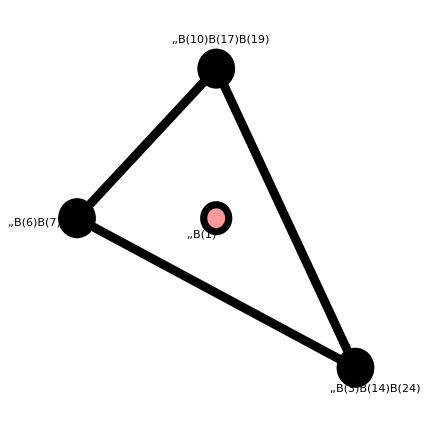

```mathematica
Map[DeleteDuplicates,Map[Simplify]@GeneratorsLattice[WC3Z3Z3]/.(Simplify@C3Z3Z3FieldGenRules)]
PolytopePlot[Keys@%,"PolytopeCellLabel"->Normal@Map[Row[#,","]&]@KeyMap[Point]@%]
```

```mathematica
C3Z3Z3Def1FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WC3Z3Z3Def1],Equal@@@C3Z3Z3Def1FieldGenRules],FieldCases@WC3Z3Z3Def1]
```

B[1] B[3]==B[1] B[14]&&B[1] B[6]==B[1] B[7]&&B[3] B[6]==B[7] B[14]&&B[3] B[7]==B[7] B[14]&&B[1] B[10]==B[1] B[19]&&B[3] B[10]==B[14] B[19]&&B[6] B[10]==B[7] B[19]&&B[7] B[10]==B[7] B[19]&&B[6] B[14]==B[7] B[14]&&B[10] B[14]==B[14] B[19]&&B[1] B[17]==B[1] B[19]&&B[3] B[17]==B[14] B[19]&&B[6] B[17]==B[7] B[19]&&B[7] B[17]==B[7] B[19]&&B[14] B[17]==B[14] B[19]&&B[3] B[19]==B[14] B[19]&&B[6] B[19]==B[7] B[19]&&B[7] B[14] B[19]==B[1]^2 (B[1]+μ B[14])&&B[1] B[26]==B[1] B[7]&&B[3] B[26]==B[7] B[14]&&B[10] B[26]==B[7] B[19]&&B[14] B[26]==B[7] B[14]&&B[17] B[26]==B[7] B[19]&&B[19] B[26]==B[7] B[19]

```mathematica
ReverseSortBy[LeafCount]@PrimaryDecompositionM2[C3Z3Z3Def1FieldChiralIdeal,DeleteCases[μ]@Variables@C3Z3Z3Def1FieldChiralIdeal]
MinimalPresentationM2[First[%],DeleteCases[μ]@Variables@C3Z3Z3Def1FieldChiralIdeal]
First[%]
```

{{B[17]-B[19],B[10]-B[19],B[7]-B[26],B[6]-B[26],B[3]-B[14],B[1]^3+μ B[1]^2 B[14]-B[14] B[19] B[26]},{B[26],B[19],B[17],B[10],B[7],B[6],B[1]},{B[26],B[14],B[7],B[6],B[3],B[1]},{B[19],B[17],B[14],B[10],B[3],B[1]}}

{{B[1]^3+μ B[1]^2 B[14]-B[14] B[19] B[26]},{B[3]→B[14],B[6]→B[26],B[7]→B[26],B[10]→B[19],B[17]→B[19]}}

{B[1]^3+μ B[1]^2 B[14]-B[14] B[19] B[26]}